```mathematica
rawfig2a=Import[NotebookDirectory[]<>"fig2a_data.csv","CSV"];
```

## Equilibrium calculation

```mathematica
A[u_,α_,γ_]:=(u/(1-u)+1-γ)/(α γ);
equilibrium[r_,β_,u_,α_,γ_]:=1/(((r+1)/(A[u,α,γ] (r-1)+r))^(1/β)+1);
```

## Fig2a

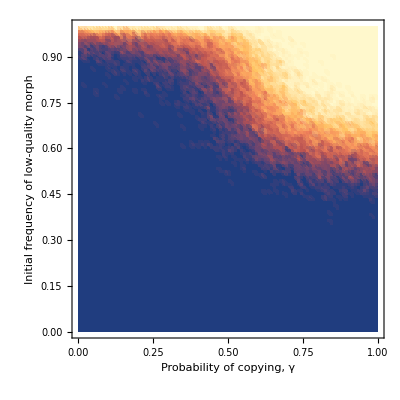

```mathematica
ListDensityPlot[rawfig2a⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

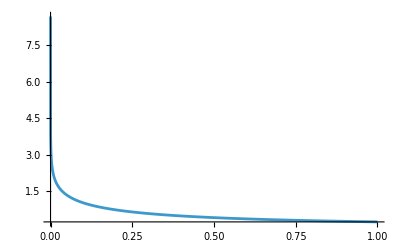

```mathematica
q2=3;q1=2;β=2;u=0.01;α=0.8;
Plot[equilibrium[q2/q1,β,u,α,γ],{γ,0,1},PlotRange->All]
```

## Fig2b

```mathematica
rawfig2b=Import[NotebookDirectory[]<>"fig2b_data.csv","CSV"];
```

```mathematica
rawfig2b⟦2;;10⟧
```

{{0.,0.,0.},{0.,0.01,0.0005},{0.,0.02,0.004},{0.,0.03,0.006},{0.,0.04,0.0075},{0.,0.05,0.0085},{0.,0.06,0.0095},{0.,0.07,0.0105},{0.,0.08,0.011}}

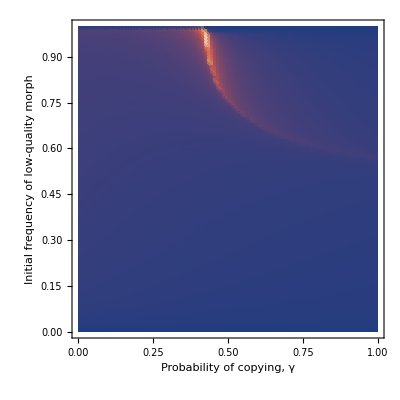

```mathematica
ListDensityPlot[rawfig2b⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Normalised fixation time",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

## Fig 2c

```mathematica
rawfig2c=Import[NotebookDirectory[]<>"fig2c_data.csv","CSV"];
```

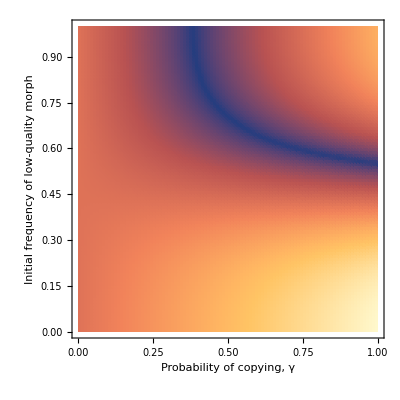

```mathematica
ListDensityPlot[rawfig2c⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Absolute difference in modified qualities",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```